```mathematica
SetDirectory@NotebookDirectory[]
```

C:\Users\prosa_000\Desktop\bionic_eye\Assets

```mathematica
range=2;
res=255;
gaus=PDF[NormalDistribution[]];
Clamp[x_]:=Max[0,Min[x,1]]

depth=10*y;

(*ass*)
pts={{0,1},{0.3,0.95},{0.5,0.8},{2,0.4},{3,0.3},{5,0.15},{10,0}}

(*indoors*)
pts={{0,1},{0.3,0.95},{0.5,0.8},{2,0.4},{3,0.2},{5,0.1},{10,0}}

df=Interpolation[pts,InterpolationOrder->1];
Abs[1 - y^0.2 + y/100]
dll=df[depth]^2;

f=(dll*(0.5+gaus[x]/gaus[0])*(1-x));
f=dll*(1-x);
img=Image[N@Table[f, {y,0,1,1/res},{x, 0, range, range/res}]]
Export["Fx/falloff.bmp",img]
```

{{0,1},{0.3,0.95},{0.5,0.8},{2,0.4},{3,0.3},{5,0.15},{10,0}}

{{0,1},{0.3,0.95},{0.5,0.8},{2,0.3},{3,0.2},{5,0.1},{10,0}}

Abs[1-y^0.2+y/100]

-Graphics-

Fx/falloff.bmp

```mathematica
N[Sqrt[2]]
```

1.41421

{{0,1},{0.1,1},{0.5,0.5},{1,0.24},{5,0.1},{10,0}}

(-10+x) (-1/10+(0.016+(-0.0143333+(0.00632749+0.07043 (-0.5+x)) (-1+x)) (-5+x)) x)

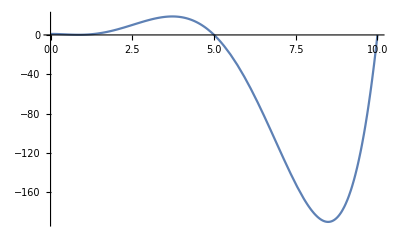

```mathematica
(*pts={{1/0.1,1},{1/0.5,0.5},{1/10,0}};*)
b=InterpolatingPolynomial[pts,x]
Plot[b,{x,0,10}]
(*b=BSplineFunction[pts,SplineDegree->2]
ParametricPlot[b[t],{t,0,1}]*)
```

{{0,1},{0.1,1},{0.5,0.5},{1,0.24},{5,0.1},{10,0}}

InterpolatingFunction[{{0., 10.}}, <>]

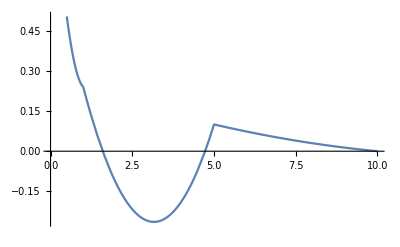

```mathematica
pts={{0,1},{0.1,1},{0.5,0.5},{1,0.24},{5,0.1},{10,0}}
Interpolation[pts,InterpolationOrder->]
Plot[%[x],{x,0,10}]
```

```mathematica
dll
```

Abs[1-y^0.2+y/100]

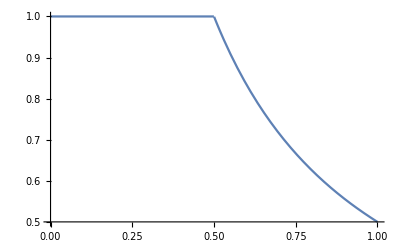

```mathematica
Plot[Min[1,0.5/x],{x,0,1}]
```